```mathematica
Clear["Global`*"]
SetDirectory["/Users/brycemorsky/Desktop/New projects/Norms and pandemics/figures"];
SetOptions[{Plot,ParametricPlot,ListPlot,ListLinePlot,ListPlot3D},PlotTheme->"Vibrant",BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->Thickness[0.008]];
```

```mathematica
g[p_]=1/(1+p^η);
g[p_]=1-η*p;
u[i_,p_,q_,c_] = -β*g[p]*i-c*p-θ*(p-q)^2;
BRD[i_,p_,c_]=1/(1+Exp[κ*(u[i,0,p,c]-u[i,1,p,c])])-p;
RD[i_,p_,c_]=p*(1-p)*(u[i,1,p,c]-u[i,0,p,c]);
(* A couple different utility differences (between obeying or disobeying the norm. *)
SEIR={s1'[t]==-β*g[p1[t]]*s1[t]*i[t],s2'[t]==-β*g[p2[t]]*s2[t]*i[t],e'[t]==β*(g[p1[t]]*s1[t]+g[p2[t]]*s2[t])*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p1'[t]== ϵ*BRD[i[t],p1[t],c1],p2'[t]== ϵ*BRD[i[t],p2[t],c2]};
ics={s1[0]==0.69,s2[0]==0.3,e[0]==0,i[0]==0.01,p1[0]==0.01,p2[0]==0.01};
SEIRS={s1'[t]==-β*g[p1[t]]*s1[t]*i[t]+α*(1-s1[t]-s2[t]-e[t]-i[t]),s2'[t]==-β*g[p2[t]]*s2[t]*i[t]+α*(1-s1[t]-s2[t]-e[t]-i[t]),e'[t]==β*(g[p1[t]]*s1[t]+g[p2[t]]*s2[t])*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p1'[t]== ϵ*BRD[i[t],p1[t],c1],p2'[t]== ϵ*BRD[i[t],p2[t],c2]};
ics={e[0]==0,i[0]==0.01,p1[0]==0.01,p2[0]==0.01};
```

```mathematica
eqs=FullSimplify[Solve[{-β*g[p]*s*i+α*(1-s-e-i)==0,β*g[p]*s*i-δ*e==0,δ*e-γ*i==0,ϵ*RD[i,p]==0},{s,e,i,p}]]
D[{-β*g[p]*s*i+α*(1-s-e-i),β*g[p]*s*i-δ*e,δ*e-γ*i,ϵ*RD[i,p]},{{s,e,i,p}}]/.eqs
```

```mathematica
(* Parameters *)
α=0.01;
β=0.41;
γ=0.1;
δ=0.2;
ϵ=1;
κ=100;
(*c=0.025;*)
θ=0.03;
(*η=0.8;*)
```

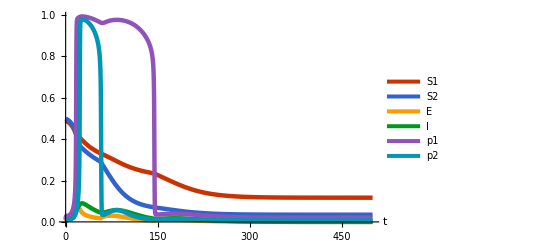

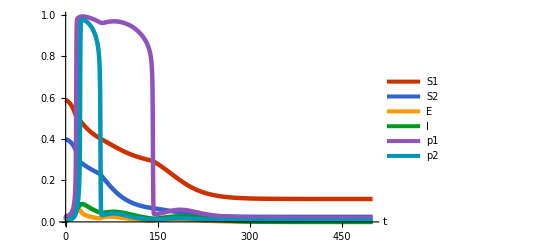

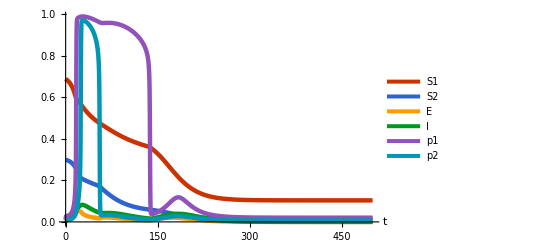

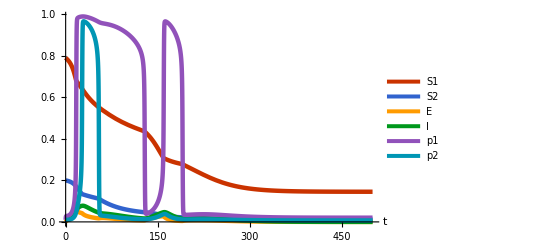

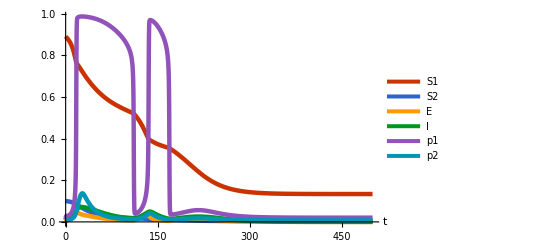

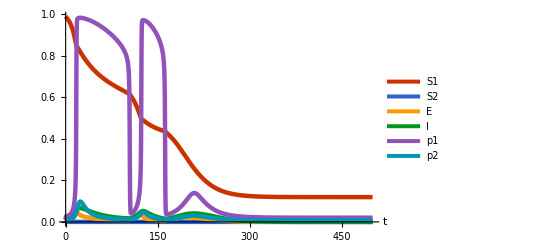

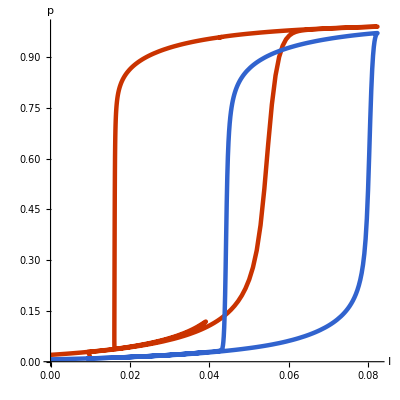

```mathematica
sol1=NDSolve[Join[SEIR/.{c1->0.01,c2->0.02,η->0.8},{s1[0]==0.49,s2[0]==0.5},ics],{s1,s2,e,i,p1,p2},{t,0,1000}];
plt1=Plot[Evaluate[{s1[t],s2[t],e[t],i[t],p1[t],p2[t]}/.sol1],{t,0,500},PlotRange->All,PlotLegends->{"S1","S2","E","I","p1","p2"},AxesLabel->{"t"}]
sol2=NDSolve[Join[SEIR/.{c1->0.01,c2->0.02,η->0.8},{s1[0]==0.59,s2[0]==0.4},ics],{s1,s2,e,i,p1,p2},{t,0,1000}];
plt2=Plot[Evaluate[{s1[t],s2[t],e[t],i[t],p1[t],p2[t]}/.sol2],{t,0,500},PlotRange->All,PlotLegends->{"S1","S2","E","I","p1","p2"},AxesLabel->{"t"}]
sol3=NDSolve[Join[SEIR/.{c1->0.01,c2->0.02,η->0.8},{s1[0]==0.69,s2[0]==0.3},ics],{s1,s2,e,i,p1,p2},{t,0,1000}];
plt3=Plot[Evaluate[{s1[t],s2[t],e[t],i[t],p1[t],p2[t]}/.sol3],{t,0,500},PlotRange->All,PlotLegends->{"S1","S2","E","I","p1","p2"},AxesLabel->{"t"}]
sol4=NDSolve[Join[SEIR/.{c1->0.01,c2->0.02,η->0.8},{s1[0]==0.79,s2[0]==0.2},ics],{s1,s2,e,i,p1,p2},{t,0,1000}];
plt4=Plot[Evaluate[{s1[t],s2[t],e[t],i[t],p1[t],p2[t]}/.sol4],{t,0,500},PlotRange->All,PlotLegends->{"S1","S2","E","I","p1","p2"},AxesLabel->{"t"}]
sol5=NDSolve[Join[SEIR/.{c1->0.01,c2->0.02,η->0.8},{s1[0]==0.89,s2[0]==0.1},ics],{s1,s2,e,i,p1,p2},{t,0,1000}];
plt5=Plot[Evaluate[{s1[t],s2[t],e[t],i[t],p1[t],p2[t]}/.sol5],{t,0,500},PlotRange->All,PlotLegends->{"S1","S2","E","I","p1","p2"},AxesLabel->{"t"}]
sol6=NDSolve[Join[SEIR/.{c1->0.01,c2->0.02,η->0.8},{s1[0]==0.99,s2[0]==0},ics],{s1,s2,e,i,p1,p2},{t,0,1000}];
plt6=Plot[Evaluate[{s1[t],s2[t],e[t],i[t],p1[t],p2[t]}/.sol6],{t,0,500},PlotRange->All,PlotLegends->{"S1","S2","E","I","p1","p2"},AxesLabel->{"t"}]
plt7=ParametricPlot[Evaluate[{{i[t],p1[t]},{i[t],p2[t]}}/.sol3],{t,0,500},PlotRange->Full,AspectRatio->1,AxesLabel->{"I","p"}]
Export["pltbi1.png",plt1,ImageResolution->200];
Export["pltbi2.png",plt2,ImageResolution->200];
Export["pltbi3.png",plt3,ImageResolution->200];
Export["pltbi4.png",plt4,ImageResolution->200];
Export["pltbi5.png",plt5,ImageResolution->200];
Export["pltbi6.png",plt6,ImageResolution->200];
Export["pltbi7.png",plt7,ImageResolution->200];
```

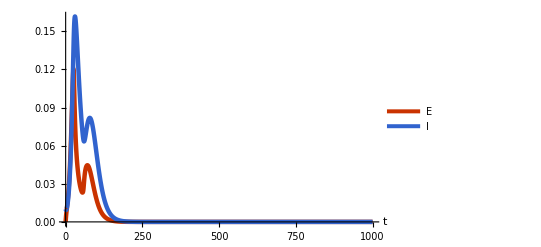

-Graphics-

-Graphics-

```mathematica
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.79},ics],{e,i},{t,0,1000}];
Plot[Evaluate[{e[t],i[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"E","I"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.79},ics],{e,i},{t,0,1000}];
Plot[Evaluate[{e[t],i[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"E","I"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.79},ics],{e,i},{t,0,1000}];
Plot[Evaluate[{e[t],i[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"E","I"},AxesLabel->{"t"}]
```

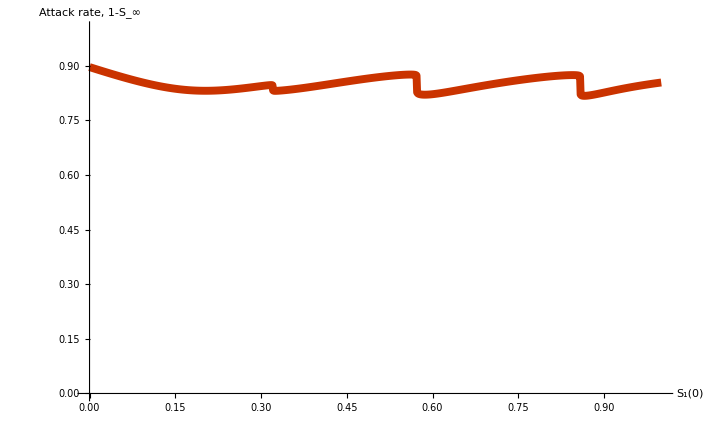

```mathematica
sfin=Array[n,{1001,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{c1->0.01,c2->0.02,η->0.9,s10->j/1000},{s1[0]==j/1000,s2[0]==1-j/1000},ics],{s1,s2,e,i,p1,p2},{t,0,1000}];
sfin[[count]]= Join[{j/1000},Evaluate[{1-s1[1000]-s2[1000]}/.sol][[1]]];
count=count+1;
,{j,0,1000}];
plt5=ListLinePlot[sfin,AxesLabel->{"S_1(0)","Attack rate, 1-S_∞"},PlotRange->{{0,1},{0,1}},BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->Thickness[0.008]]
Export["attackrate_bimod_eta09_lin_BR.png",plt5,ImageResolution->200];
```

```mathematica
sfin=Array[n,{9990,3}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{c1->0.01,c2->0.02,η->j/100},{s1[0]==k/100,s2[0]==(99-k)/100},ics],{s1,s2,e,i,p1,p2},{t,0,1000}];
sfin[[count]]= Join[{j/100},{(k-1)/100},Evaluate[{s1[1000]+s2[1000]}/.sol][[1]]];
count=count+1;
,{j,0,100},{k,0,99}];
plt7 = ListPlot3D[sfin,AxesLabel->{"η","S_1(0)","S_1+S_2"}]
(*Export["plt7RD.png",plt7,ImageResolution->200];*)
```

$Aborted

```mathematica
plt7 = ListPlot3D[sfin,AxesLabel->{"η","S_1(0)","S_1+S_2"}]
```

-Graphics3D-

```mathematica
Export["pltbimodalSEIR.png",plt7,ImageResolution->200]
```

```mathematica
ListPlot3D[sfin,AxesLabel->{"η","S_1(0)","S_1+S_2"}]
```

-Graphics3D-

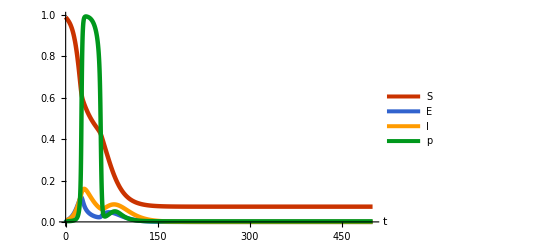

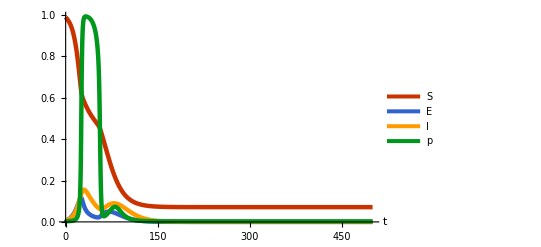

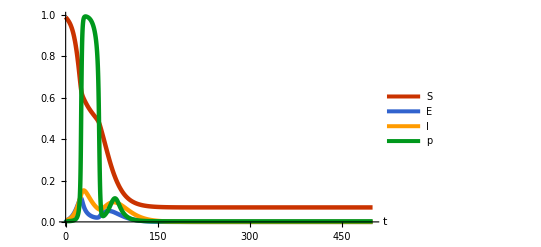

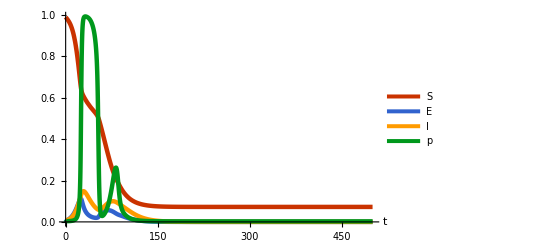

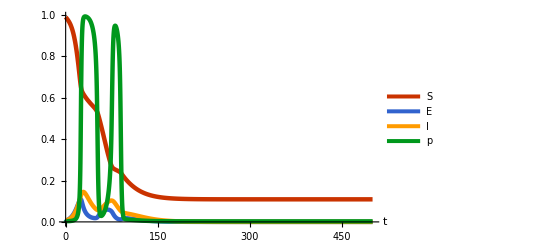

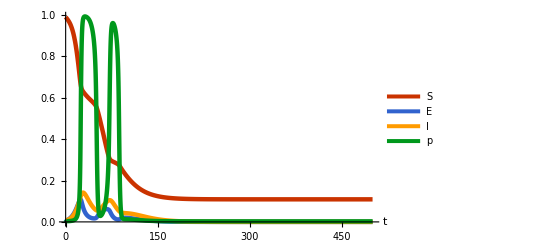

```mathematica
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.8},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.82},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.84},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.86},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.88},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.9},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
```

```mathematica
sfin=Array[n,{1001*51,3}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{c->k/1000,η->j/1000},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{0.001*j},{0.001*k},Evaluate[{s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,1000},{k,0,50}];
plt7 = ListPlot3D[sfin,AxesLabel->{"m","c","S"}]
Export["plt7RD.png",plt7,ImageResolution->200];
```

-Graphics3D-

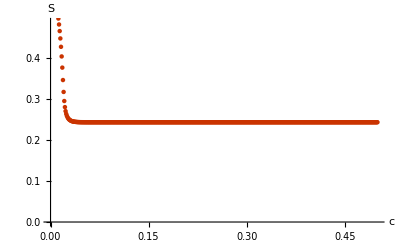

```mathematica
vtheta=Array[n,{501,2}];
count=1;
Do[
sol=NDSolve[Join[SEIRS/.{c->k/1000,η->0.8},ics],{s,e,i,p},{t,0,1000}];
vtheta[[count]]= Join[{0.001*k},Evaluate[{s[1000]}/.sol][[1]]];
count=count+1;
,{k,0,500}];
plt6=ListPlot[vtheta,PlotStyle->PointSize[0.008],AxesLabel->{"c","S"}]
Export["plt6.png",plt6,ImageResolution->200];
```

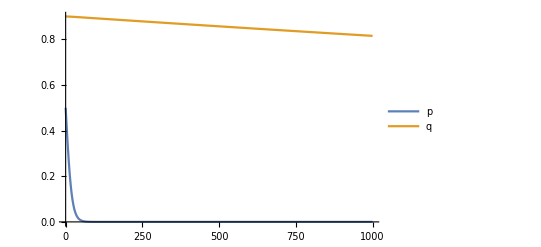

```mathematica
b=2;
c=1;
α=0.9;
ϵ=0.0001;
eqn={p'[t]==p[t]*(1-p[t])*(p[t]*(b-c+α*(1-q[t]))+(1-p[t])*(-c+α*(1-q[t]))-p[t]*(b-α*q[t])-(1-p[t])*(-α*q[t])),q'[t]==ϵ*(p[t]-q[t])};
ic={p[0]==0.5,q[0]== 0.9};
sols=NDSolve[Join[eqn,ic],{p,q},{t,0,1000}];
Plot[Evaluate[{p[t],q[t]}/.sols],{t,0,1000},PlotRange->All,PlotLegends->{"p","q"},AxesLabel->{"t"}]
```

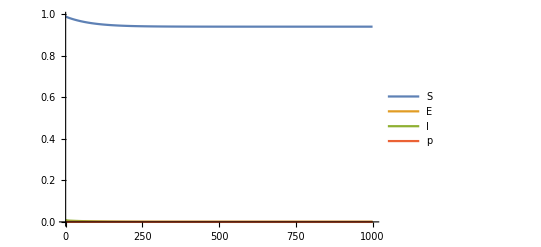

```mathematica
sol=NDSolve[Join[{s'[t]==-β*(1-m)*s[t]*i[t],e'[t]==β*(1-m)*s[t]*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p'[t]== ϵ*(1/(1+Exp[-100*(p[t]+θ*i[t]-1)])-p[t])}/.{m->0.79,c->20},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
```